## Notes

This program extracts Apple Health data (.csv format)  and graphs and analyzes heart rate data.

## Inputting, Formatting, and Extracting Useful Data from File

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Connie\Downloads\Summer2018Starter-master\Summer2018Starter-master\Summer2018

```mathematica
heartRate= Import["HKQuantityTypeIdentifierHeartRate.csv","CSV"];
```

```mathematica
(* extracts last column of data (heart rate)*)
getImportantData[ entries_List ]:= Part[ entries , All, -1];

(* gets second to last column in the data (time) *)
getDateString[ entry_String ]:= Part [ StringSplit[ entry ,";"] , -2] ;

(* gets 2nd to last column of data which is heart rate value as a Number *)
getHeartRate[ entry_String ]:= ToExpression [Part [ StringSplit[ entry ,";"] , -1]] ;
```

```mathematica
(* example: *)
```

```mathematica
getDateString ["software:3.1>;count/min;2017-02-06 20:00:03 -0400;2017-02-06 19:58:53 -0400;2017-02-06 19:58:53 -0400;61"]
```

2017-02-06 19:58:53 -0400

```mathematica
(* Dropping the first line, extract all rows and columns of heartrate data: *)
```

```mathematica
getImportantData[Drop[heartRate,1]]
```

{software:3.1>;count/min;2017-02-06 20:00:03 -0400;2017-02-06 19:58:53 -0400;2017-02-06 19:58:53 -0400;61,257626,software:4.3.1>;count/min;2018-07-04 14:30:46 -0400;2018-07-04 14:25:36 -0400;2018-07-04 14:25:36 -0400;71}
 |  |  |  |

```mathematica
(* Put in one time entry as formatted by apple watch, output DateObject to use to plot Mathematica *)
 getDateObject[ timeEntry_String ] := 
                                    With[ { extractTZ = StringTake[ timeEntry , {-5,-1} ] },
                                    
                                           timeZoneString = StringJoin[" GMT-", ToString[ (Interpreter["Number"][StringTake[extractTZ,{2,3}]])] ];
                                           
                                           DateObject[ StringDrop[ timeEntry , -5]
                                                         ]
                                         ];
                                         
  (* Apply getDateObject on all time datapoints *)
  (* Generate time column to plot heart rate data with *)
  getAllDateObjects [  entries_List ] := Map [ 
                                                 getDateObject[ 
                                                                getDateString [ # ]
                                                              ] &
                                                   ,
                                                   getImportantData[ entries ]
                                               ];
                                                   
 (* Generate heart rate column to plot *)
  getAllHeartPoints [  entries_List ] := Map [  
                                                getHeartRate
                                                , 
                                                getImportantData[ entries ] 
                                              ] ;
```

## Plot data

```mathematica
getAllDateObjects [Drop[heartRate,1]]
```

{Mon 6 Feb 2017 19:58:53GMT-4.,Mon 6 Feb 2017 20:03:21GMT-4.,Mon 6 Feb 2017 20:06:30GMT-4.,Mon 6 Feb 2017 20:12:08GMT-4.,257620,Wed 4 Jul 2018 14:11:05GMT-4.,Wed 4 Jul 2018 14:16:59GMT-4.,Wed 4 Jul 2018 14:22:11GMT-4.,Wed 4 Jul 2018 14:25:36GMT-4.}
 |  |  |  |

```mathematica
heartRatePoints = getAllHeartPoints [ Drop[heartRate,1]]
```

{61,60,58,61,55,53,52,51,49,49,49,49,49,49,51,51,52,53,54,54,54,59,61,51,51,51,50,51,52,52,53,53,49,51,54,52,53,52,49,49,49,52,53,51,51,51,52,58,257532,65,65,63,65,60,64,65,70,65,62,69,59,72,69,62,68,57,57,68,64,63,62,63,66,71,66,76,70,68,77,94,81,80,68,67,79,83,75,81,82,69,71,77,79,68,75,70,71}
 |  |  |  |

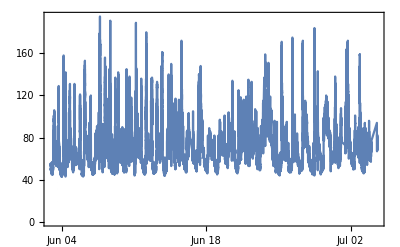

```mathematica
DateListPlot [ Take[Transpose[{dateObjects,heartRatePoints}],-25000]]
```

```mathematica
dateObjects= %131 ;
```

```mathematica
dateObjects [[1]]
```

Mon 6 Feb 2017 19:58:53GMT-4.

```mathematica
SetDirectory[NotebookDirectory []]
```

C:\Users\Connie\Downloads\Summer2018Starter-master\Summer2018Starter-master\Summer2018

```mathematica
Export ["DateObject.mx", dateObjects ,"MX" ]
```

DateObject.mx

```mathematica
dobjs=Import["DateObject.mx"];
```

```mathematica
getAllDateObjects[]
```

## Analysis

```mathematica
(* PLAN OUTLINE *)
```

```mathematica
(*________________ Part I: Look at irregular data: identify potential stress factors ____________________________*)
(* Exclude all data that falls within the range of healthy sample user (with options to choose age group and gender) *)
(* Identify instances of possible stress from times of out of range heart rate *)
(* Match up times of irregular heart rate with time of which activities were indicated from daily log *)
(* Purpose: allow people to increase their noninvasive retrospective self tracking capabilities *)
(* Emotions are one factor that determine heart rate :
 http://www.heart.org/HEARTORG/Conditions/HighBloodPressure/GettheFactsAboutHighBloodPressure/All-About-Heart-Rate-Pulse_UCM_438850_Article.jsp#.W0EdqbgnZEY
```

```mathematica
(*_________________ Part II: Determine resting heart rate: make exercise recommendations and print stats____________ *)
https://www.health.harvard.edu/blog/resting-heart-rate-can-reflect-current-future-health-201606179806
```

```mathematica
(* Ask the user to follow instructions to determine his/her resting heart rate by following instructons and then inputting the number in a field on the website *)

(* _________________Part IB: Daily logs/questionaire answers_____________________________________________*)
(* Extract activities in log and moods*)
(* Make list of sentiments from using Classify functon on all sentences in each log *)
(* How to implement machine learning to learn moods and apply across the heart rate data *)
```

## Web Options

```mathematica
(* drop down menu for user to select age group and gender ?*)
```